```mathematica
3+4
```

7

```mathematica
q = {qx, qy}
n1 = {1/2,Sqrt[3]/2}
n2 = {-1/2, Sqrt[3]/2}
```

{qx,qy}

{1/2,(√3)/2}

{-1/2,(√3)/2}

```mathematica
f = 2(Jx Exp[ i Sum[ Part[q,j]Part[n1, j],{j, 1,2}] ] + Jy Exp[ i Sum[ Part[q,k]Part[n2, k],{k, 1,2}] ] + Jz)
```

2 (ⅇ^(i (qx/2+(√3 qy)/2)) Jx+ⅇ^(i (-qx/2+(√3 qy)/2)) Jy+Jz)

```mathematica
Clear[Energy, f]
f = 2(Jx Exp[ i Sum[ Part[q,j]Part[n1, j],{j, 1,2}] ] + Jy Exp[ i Sum[ Part[q,k]Part[n2, k],{k, 1,2}] ] + Jz)
Energy = Abs[f]
Manipulate[Evaluate[Energy],{qx, -10, 10}, {qy, -10, 10}, {Jx, -10, 10}, {Jy, -10, 10},{Jz, -10, 10}]
```

2 (ⅇ^(i (qx/2+(√3 qy)/2)) Jx+ⅇ^(i (-qx/2+(√3 qy)/2)) Jy+Jz)

2 Abs[ⅇ^(i (qx/2+(√3 qy)/2)) Jx+ⅇ^(i (-qx/2+(√3 qy)/2)) Jy+Jz]

Some restrictions to Jx,  Jy, and, Jz exist, for example they must satisfy the Triangle Inequalities,

					|Jx| < |Jy| + |Jz|,
                    
					|Jy| < |Jx| + |Jz|,
                    
					|Jz| < |Jy| + |Jx|.
                    
Also, Jx + Jy + Jz = 1.

```mathematica
Clear[Jx, Jy, Jz,Energy, f]
Jx = 1/3
Jy = 1/3
Jz = 1/3

f[qx,qy] = N[2(Jx Exp[ I Sum[ Part[q,j]Part[n1, j],{j, 1,2}] ] + Jy Exp[ I Sum[ Part[q,k]Part[n2, k],{k, 1,2}] ] + Jz)]

Energy[qx,qy] = Evaluate[Abs[Evaluate[f[qx,qy]]]]

Plot3D[{Evaluate[Energy[qx,qy]], Evaluate[-1*Energy[qx,qy]]}, {qx, -10, 10}, {qy,-10,10}, ColorFunction -> Function[{x, y, z}, Hue[z]]]
```

1/3

1/3

1/3

2. (0.333333+0.333333 2.71828^((0.+1. ⅈ) (-0.5 qx+0.866025 qy))+0.333333 2.71828^((0.+1. ⅈ) (0.5 qx+0.866025 qy)))

2. Abs[0.333333+0.333333 2.71828^((0.+1. ⅈ) (-0.5 qx+0.866025 qy))+0.333333 2.71828^((0.+1. ⅈ) (0.5 qx+0.866025 qy))]

-Graphics3D-

```mathematica
ComplexPlot3D[(z^2 + 1)/(z^2 - 1), {z, -2 - 2 I, 2 + 2 I}, ColorFunction->"CyclicLogAbsArg"]
```

-Graphics3D-

```mathematica
(* 
Animate[  Plot3D[  {Evaluate[  Abs[  2(Jx Exp[ I Sum[ Part[q,j]Part[n1, j],{j, 1,2}] ] + Jy Exp[ I Sum[ Part[q,k]Part[n2, k],{k, 1,2}] ] + Jz)  ]  ], Evaluate[  -1*Abs[  2(Jx Exp[ I Sum[ Part[q,j]Part[n1, j],{j, 1,2}] ] + Jy Exp[ I Sum[ Part[q,k]Part[n2, k],{k, 1,2}] ] + Jz)  ]  ]  }, {qx, -10, 10}, {qy,-10,10}, ColorFunction -> Function[{x, y, z}, Hue[z]  ]  ], {{Jx,1/3}, 0, 1},{{Jy, 1/3}, 0, 1},{{Jz, 1/3}, 0, 1}, AnimationRunning->False]
 *)
```

```mathematica
Clear[Jx, Jy, Jz, x, f, qx , qy, x, k1, k2, n1, n2, f1, f2, points]

(* 
k1 = {2 Pi / Sqrt[3],  2 Pi};
k2 = {2 Pi / Sqrt[3], -2 Pi};
*)

(*
Explicit expression for absolute value of g[...],
*)

Clear[n1, n2];

n1 = {Sqrt[3]/2, 1/2 };
n2 = {Sqrt[3]/2,-1/2};

energy[Jx_, Jy_, Jz_, x_, k1_, k2_] := N[2 Sqrt[Jx^2 + Jy^2 + Jz^2 + 2 Jx Jy Cos[(k1 + (k2 - k1)*x).(n1 - n2)] + 2 Jz Jx Cos[(k1 + (k2 - k1)*x).n1] + 2 Jz Jy Cos[(k1 + (k2 - k1)*x).n2]  ]  ];

energy2[Jx_, Jy_, Jz_, qx_, qy_] := N[2 Sqrt[Jx^2 + Jy^2 + Jz^2 + 2 Jx Jy Cos[{qx, qy}.(n1 - n2)] + 2 Jz Jx Cos[{qx, qy}.n1] + 2 Jz Jy Cos[{qx, qy}.n2]  ]  ];

Plot3D[{energy2[1/3, 1/3, 1/3, qx, qy], -energy2[1/3, 1/3, 1/3, qx, qy]}, {qx, -2 Pi, 2 Pi}, {qy, -2 Pi, 2 Pi}, ImageSize->1000, PlotPoints->100, ColorFunction -> Function[{x, y, z}, Hue[z]  ]]

(* This is a general function which describes moving from one position in the Brillouin zone to another *)
g[Jx_, Jy_, Jz_, x_, k1_, k2_] := N[Abs[2 (Jx Exp[I (k1 + ((k2 - k1)*x)). n1 ] + Jy Exp[I (k1 + ((k2 - k1)*x)) . n2] + Jz)]];


points = 500;
Manipulate[ListLinePlot[{Join[ Table[g[Jx, Jy, Jz, x, {0, 0}, {   2 Pi / Sqrt[3],2 Pi / 3}], {x, 0, 1, 1/points}], Table[g[Jx, Jy, Jz, x-1, { 2 Pi / Sqrt[3], 2 Pi / 3 }, { 2 Pi / Sqrt[3], - 2 Pi / 3}], {x, 1, 2, 1/points}], Table[g[Jx, Jy, Jz, x-2, {  2 Pi / Sqrt[3], - 2 Pi / 3 }, {0,0}], {x, 2, 3, 1/points}]], Join[ Table[-g[Jx, Jy, Jz, x, {0, 0}, {  2  Pi / Sqrt[3],2 Pi / 3}], {x, 0, 1, 1/points}], Table[-g[Jx, 1/3, Jz, x-1, { 2 Pi / Sqrt[3], 2 Pi / 3 }, { 2 Pi / Sqrt[3], - 2 Pi / 3}], {x, 1, 2, 1/points}], Table[-g[Jx, Jy, Jz, x-2, {  2 Pi / Sqrt[3], - 2 Pi / 3 }, {0,0}], {x, 2, 3, 1/points}]] }, ImageSize->1000], {{Jx, 1/3}, 0, 1}, {{Jy, 1/3}, 0, 1}, {{Jz, 1/3}, 0, 1}]
```

-Graphics3D-

Table::iterb: Iterator {x,0,1,1/points} does not have appropriate bounds.

Table::iterb: Iterator {x,1,2,1/points} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::nliter: Non-list iterator g[FE`Jx$$46,FE`Jy$$46,FE`Jz$$46,x-1,{(2 π)/(√3),(2 π)/3},{(2 π)/(√3),-(2 π)/3}] at position 3 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator -g[FE`Jx$$46,1/3,FE`Jz$$46,x-1,{(2 π)/(√3),(2 π)/3},{(2 π)/(√3),-(2 π)/3}] at position 3 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator g[FE`Jx$$46,FE`Jy$$46,«3»,{2. (3.141592653589793 0.5773502691896258),-2. (3.141592653589793 0.3333333333333333)}] at position 3 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

So this has successfully modelled the situation where there are no vortices in the lattice, and we have produced a hexagonal Brillouin zone as expected. The next step is to apply the calculations to ribbons of the lattice, so that one can simply sum over the ribbons in the lattice to achieve a result. 
The ribbon calculations produce a matrix equation, which one has to solve to find the eigenvalues, once these eigenvalues are found one can then plot their functions. The eigenvalue matrix looks like so,

																						(  0         -t Gk         0            0         . . .  )    (  Psi_{1, A} )                       (  Psi_{1, A}  )
																						(  -t Gk       0         - t            0         . . .  )    (  Psi_{1, B} )                       (  Psi_{1, B}  ) 
																						(  0            - t           0         -t Gk     . . .  )    (          :          )       =       E    (          :           )
																						(   :              0         -t Gk       0         . . .  )    (  Psi_{N, A} )                      (  Psi_{N, A} )
																						(   :               :            :             :          . . .  )    ( Psi_{N, B}  )                      (  Psi_{N, B} )


So we need to find the eigenvalues of the matrix on the left, where Gk = 2Cos(ka/2) where a is the ribbon separation, and can be set equal to 1. Note that t = Jx = Jy = Jz, so this is the symmetric situation. We thus need a general way of forming the matrix in order to find the eigenvalues for a given number of sites in the ribbon.

We start by considering the case where we have no vortices in the nanoribbon.

{}

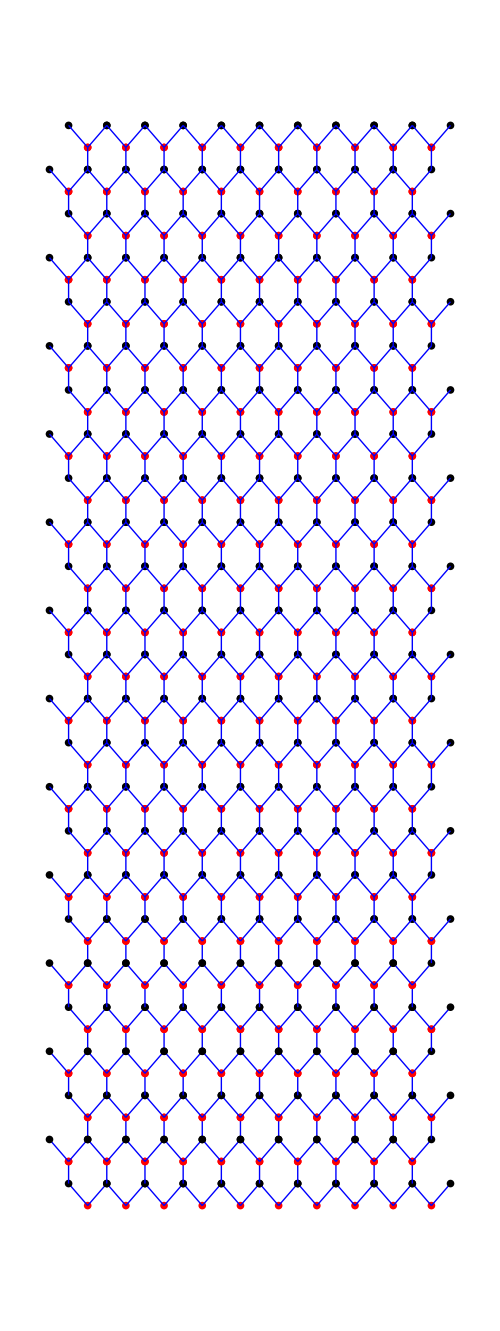

SparseArray[…]

```mathematica
Clear[EnergyMatrix, EnergyMatrix2, points, NumberOfSites, ExponentialTermLocations, HoppingTermLocations, EnergyEigenvalues]
NumberOfSites = 50;
VortexIndex = 5;
points = 10;

ExponentialTermLocations = {};
ConjugateExponentialTermLocations = {};
HoppingTermLocations =  {};

For[i = 0, i <  NumberOfSites/2,  i++, 
AppendTo[ExponentialTermLocations, {1 + 2 i, 2 + 2i}];
AppendTo[ConjugateExponentialTermLocations, {2 + 2 i, 1 + 2i}];
If[3 + 2i < NumberOfSites, 
AppendTo[HoppingTermLocations, {3+2i, 2+2i}];
AppendTo[HoppingTermLocations, {2+2i, 3+2i}];
,Null]
]


EnergyMatrix[k_,t_]:=SparseArray[Flatten[Append[{{ExponentialTermLocations}},{ConjugateExponentialTermLocations, HoppingTermLocations}],2]-> Flatten[Append[{{Table[-t * (1 + Exp[I k]), {VortexIndex - 1}]}}, {{-t * (-1 + Exp[I k])},Table[-t * (1 + Exp[I k]), {(NumberOfSites/2) - VortexIndex}],Table[-t * (1 + Exp[-I k]), {VortexIndex-1}], {-t * (-1 + Exp[-I k])}, Table[-t * (1 + Exp[-I k]), {(NumberOfSites/2) - VortexIndex}],Table[-t , {Length[HoppingTermLocations]}]}],2]]


EnergyMatrix2[k_,t_]:=SparseArray[Flatten[Append[{{ExponentialTermLocations}},{ConjugateExponentialTermLocations, HoppingTermLocations}],2]-> Flatten[Append[{{Table[-t * (1 + Exp[I k]), {NumberOfSites/2 }]}}, {Table[-t * (1 + Exp[-I k]), {NumberOfSites/2}],Table[-t , {Length[HoppingTermLocations]}]}],2]]

CenterOfTranslation = {0,0};
a=20;
Translation1 = {a/2, 2 a Sqrt[3] /3};
Translation2 = {-a/2, 2a Sqrt[3] /3};
RelativeBsite1 = {a/2, a Sqrt[3]/3};
RelativeBsite2 = {-a/2, a Sqrt[3]/3};

GraphicsTable = {}
NumberOfRibbons = 10;

For[n = 0, n < NumberOfRibbons, n++,
CenterOfTranslation = {0,0} + {n*a,0};
For[l = 0, l < NumberOfSites - 1, l++,
If[ N[EnergyMatrix2[k,t][[1 + l,2 + l]]/.{k->1,t->1}] == - t/.{k->1,t->1}, 
{
If[l ==  0, Null,AppendTo[GraphicsTable,{Thick,Blue, Line[{CenterOfTranslation, CenterOfTranslation - {0,(Sqrt[3] a/3)}}], Red, Disk[CenterOfTranslation, 2]}]]
},
{
AppendTo[GraphicsTable,{Red, Disk[CenterOfTranslation, 2]}];
AppendTo[GraphicsTable,{Thick,Blue, Line[{CenterOfTranslation, CenterOfTranslation+RelativeBsite1}]}];
AppendTo[GraphicsTable,{Thick,Blue, Line[{CenterOfTranslation, CenterOfTranslation+RelativeBsite2}]}];
AppendTo[GraphicsTable,{Black, Disk[CenterOfTranslation + RelativeBsite1, 2]}];
AppendTo[GraphicsTable,{Black, Disk[CenterOfTranslation + RelativeBsite2, 2]}];
If[EvenQ[(l)/2],CenterOfTranslation += Translation2, CenterOfTranslation += Translation1];
}
 ]
]
]

Graphics[GraphicsTable, ImageSize->500]

EnergyMatrix[k,t]

EnergyEigenvalues[k_,t_] := Eigenvalues[N[EnergyMatrix[k,t]]]
EnergyEigenvalues2[k_,t_]:= Eigenvalues[N[EnergyMatrix2[k,t]]]
 
Plot[{Abs[Evaluate[EnergyEigenvalues[k,1/3]]], -Abs[Evaluate[EnergyEigenvalues[k,1/3]]]},{k, -Pi,  Pi}, PlotPoints->100, ImageSize->1000, AxesLabel ->{"k", "Energy"},Ticks->{ {- Pi, Pi} }] 
Plot[{Abs[Evaluate[EnergyEigenvalues2[k,1/3]]], -Abs[Evaluate[EnergyEigenvalues2[k,1/3]]]},{k, -Pi,  Pi}, PlotPoints->100, ImageSize->1000, AxesLabel ->{"k", "Energy"},Ticks->{ {- Pi, Pi} } ]
```

Next, let us consider the situation where we include vortices in the nanoribbon. This essentially corresponds with altering (1 + exp{+/- i k a } ) into (- 1 + exp{+/- i k a } ) for a given value of m, corresponding to one of the 2x2 matrices.

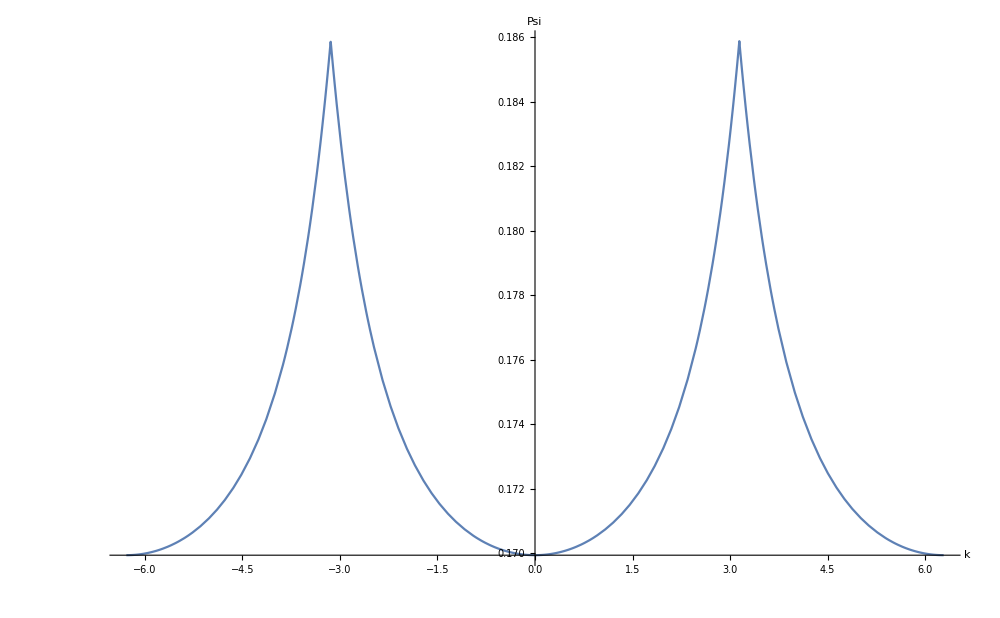

1

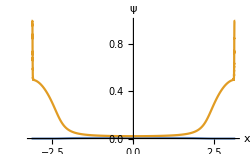

2

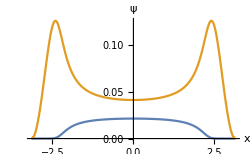

3

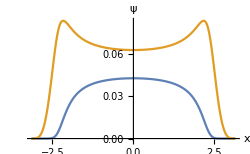

4

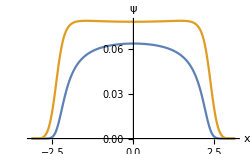

5

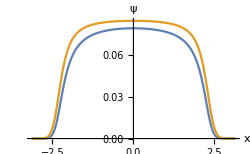

6

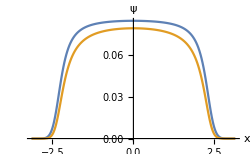

7

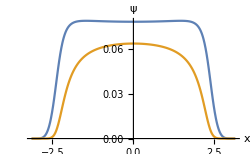

8

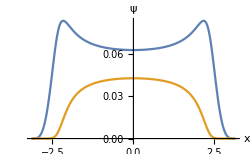

9

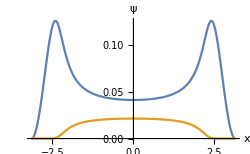

10

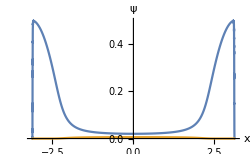

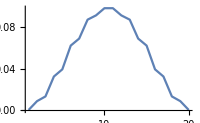

-Graphics-

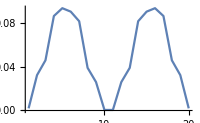

-Graphics-

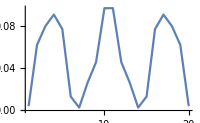

-Graphics-

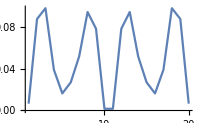

-Graphics-

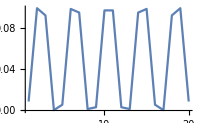

-Graphics-

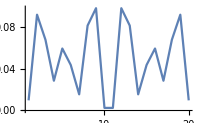

-Graphics-

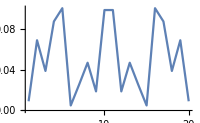

-Graphics-

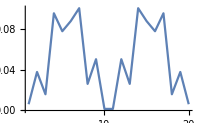

-Graphics-

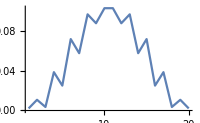

-Graphics-

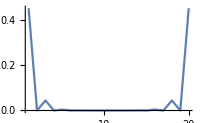

-Graphics-

```mathematica
Clear[EnergyMatrix, points, NumberOfSites, HoppingTermLocations, EnergyEigenvalues]
NumberOfSites = 20;
VortexIndex = 5;
points = 10;

ExponentialTermLocations = {};
ConjugateExponentialTermLocations = {};
HoppingTermLocations =  {};

For[i = 0, i <  NumberOfSites/2,  i++, 
AppendTo[ExponentialTermLocations, {1 + 2 i, 2 + 2i}];
AppendTo[ConjugateExponentialTermLocations, {2 + 2 i, 1 + 2i}];
If[3 + 2i < NumberOfSites, 
AppendTo[HoppingTermLocations, {3+2i, 2+2i}];
AppendTo[HoppingTermLocations, {2+2i, 3+2i}];
,Null]
]

EnergyMatrix[k_,t_]:=SparseArray[Flatten[Append[{{ExponentialTermLocations}},{ConjugateExponentialTermLocations, HoppingTermLocations}],2]-> Flatten[Append[{{Table[-t * (1 + Exp[I k]), {NumberOfSites/2 }]}}, {Table[-t * (1 + Exp[-I k]), {NumberOfSites/2}],Table[-t , {Length[HoppingTermLocations]}]}],2]];

EnergyEigenvalues[k_,t_] := Eigenvalues[N[EnergyMatrix[k,t]]];
EnergyEigenvectors[k_,t_]:= Eigenvectors[N[EnergyMatrix[k,t]]];


Plot[{Abs[EnergyEigenvectors[k,1/3]][[3,2]]},{k, - 2Pi,  2 Pi}, PlotPoints->100, ImageSize->1000, AxesLabel ->{"k", "Psi"},Ticks-> Automatic] 



For[i = 1, i < (NumberOfSites/2) + 1, i++, {Print[i];Plot[{Abs[EnergyEigenvectors[x,1/3][[-1,2 i]] ]^2, Abs[EnergyEigenvectors[x,1/3][[-1, 2i-1]] ]^2 }, {x, - Pi,  Pi}, PlotPoints->200, ImageSize->250, AxesLabel->{"x", ψ }, Ticks->Automatic, PlotRange->Full]//Print}]


For[i = 1, i < Length[EnergyEigenvectors[Pi,1/3]]+1,i++,ListLinePlot[Abs[N[EnergyEigenvectors[0.9*Pi,1/3][[i]]]]^2, ImageSize->200,PlotRange->Full]//Print]

(*
Plot[{Abs[EnergyEigenvectors[k,1/3]][[1,1]]},{k, - 2 Pi, 2 Pi}, PlotPoints->100, ImageSize->1000, AxesLabel ->{"k", "Psi"},Ticks->Automatic] 
*)
```

Eigenvalues::arh: Because finding 5000 out of the 5000 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

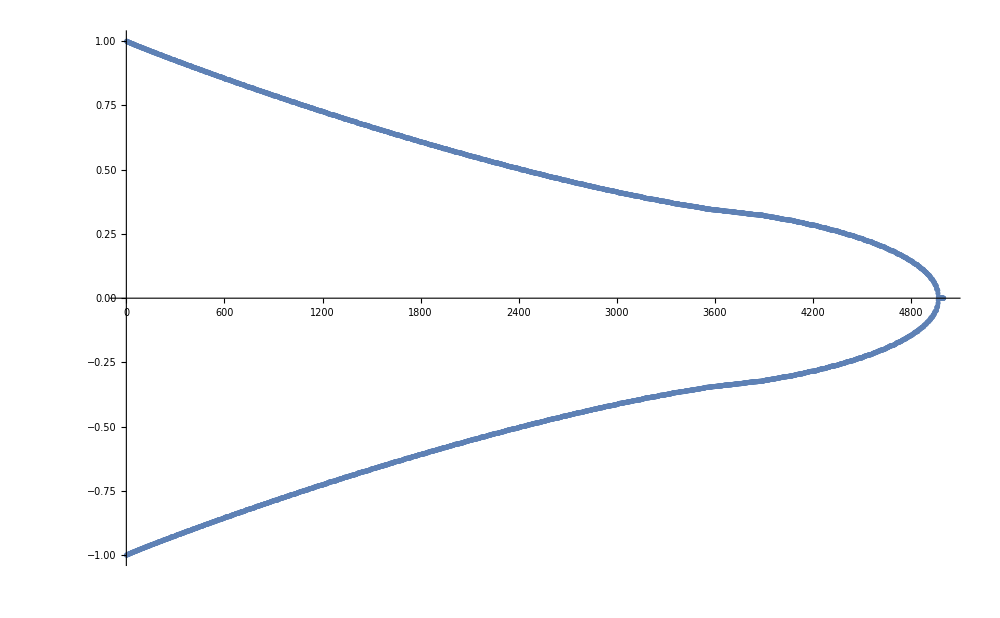

Eigenvectors::arh: Because finding 5000 out of the 5000 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvectors.

$Aborted

```mathematica
Clear[EnergyMatrix, points, NumberOfSites,NumberOfRibbons, HoppingTermLocations, EnergyEigenvalues, m]
NumberOfSites =100;
NumberOfRibbons = 50;
points = 10;
HoppingTermLocations =  {};
 
For[j = 0, j < NumberOfRibbons, j++,
m = 1;
For[i = 0, i <  NumberOfSites,  i++,
If[OddQ[ i],
(* Odd Rows *)
(* Corresponds to B Site *)
{
(* Intra-mSite interaction *)
AppendTo[HoppingTermLocations,{(j * NumberOfSites)+i + 1, (j * NumberOfSites)+i}];
(* Inter-mSite interaction *)
If[i < NumberOfSites - 1,
 AppendTo[HoppingTermLocations, {(j * NumberOfSites)+i + 1, (j * NumberOfSites)+i + 2}], 
Null
];
(* If m is odd, B site interacts with ribbon right and left ribbon if m is even *)
If[ OddQ[m],
If[j < NumberOfRibbons - 1,AppendTo[HoppingTermLocations, {(j*NumberOfSites) + i + 1, (j+1)*NumberOfSites + i}], Null]
, 
If[j > 0, AppendTo[HoppingTermLocations, {j*NumberOfSites + i+1, (j-1)*NumberOfSites + i}],  Null]
];
m +=1;
}
,
(* Even Rows *)
(* Corresponds to A Site *)
{
(* Intra-mSite interaction *)
AppendTo[HoppingTermLocations, {(j * NumberOfSites) + i + 1, (j*NumberOfSites)+i+2}];
(* Inter-mSite interaction *)
If[i>0, .
AppendTo[HoppingTermLocations, {(j * NumberOfSites) + i + 1, (j*NumberOfSites)+i}],
Null
];
(* If m is odd, B site interacts with ribbon right and left ribbon if m is even *)
If[ EvenQ[m],
If[j < NumberOfRibbons - 1, AppendTo[HoppingTermLocations, {(j*NumberOfSites) + i + 1, (j+1)*NumberOfSites + i + 2}], Null]
, 
If[j > 0, AppendTo[HoppingTermLocations, {j*NumberOfSites + i+1, (j-1)*NumberOfSites + i +2}],  Null]
];
}
]
]
]

(*
(* Left Ribbon Interaction Term *)
If[j>0 , AppendTo[HoppingTermLocations, {j*NumberOfSites + i+1, (j-1)*NumberOfSites + i + 2}], Null]
*)

(*
Right ribbon interaction term for B site;
If[j < NumberOfRibbons - 1,
AppendTo[HoppingTermLocations, {(j*NumberOfSites) + i + 1, (j+1)*NumberOfSites + i}],
Null
];
*)
 
frametickfunction[xmin_,xmax_]:={#,ToString[#/NumberOfSites]}&/@FindDivisions[{xmin,xmax,NumberOfSites}, NumberOfRibbons]

EnergyMatrix[t_] := SparseArray[HoppingTermLocations-> Table[-t, NumberOfRibbons*((3*NumberOfSites) - 2) - NumberOfSites ]];

(*
EnergyMatrix[t] //MatrixForm
*)

EnergyEigenvalues[t_] := Eigenvalues[N[EnergyMatrix[t]]];
EnergyEigenvectors[t_]:=Eigenvectors[N[EnergyMatrix[t]]];

ListPlot[EnergyEigenvalues[1/3], ImageSize->1000]
ListLinePlot[{Abs[EnergyEigenvectors[1/3][[-1]]]^2}, ImageSize->1000,PlotRange->Full]

(*
For[i = 1, i < Length[EnergyEigenvectors[1/3]]+1,i++,ListLinePlot[Abs[N[EnergyEigenvectors[1/3][[i]]]]^2, ImageSize->200,PlotRange->Full,Ticks->{frametickfunction[0,NumberOfSites * NumberOfRibbons]}, GridLines->{Automatic, None}]//Print]
```

ClearAll

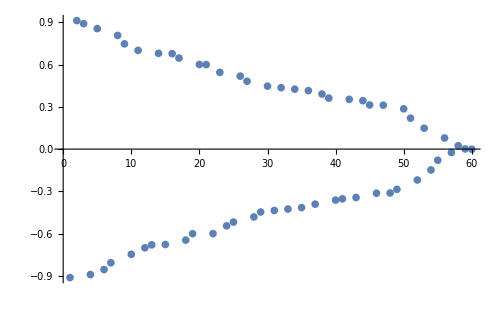

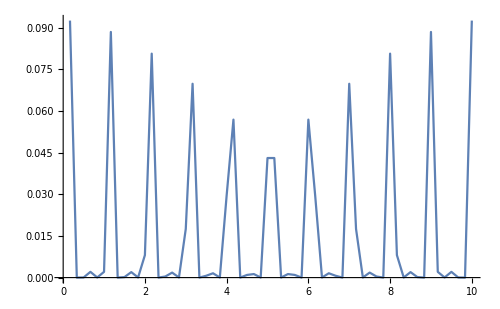

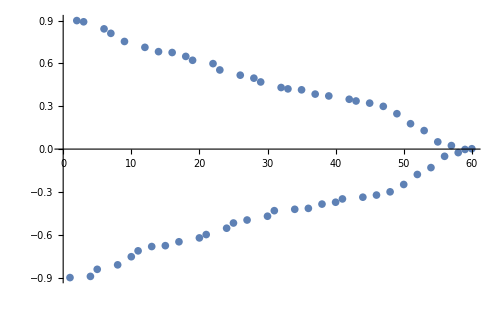

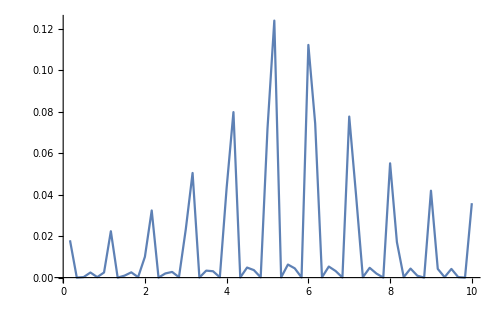

Vortex Free Case

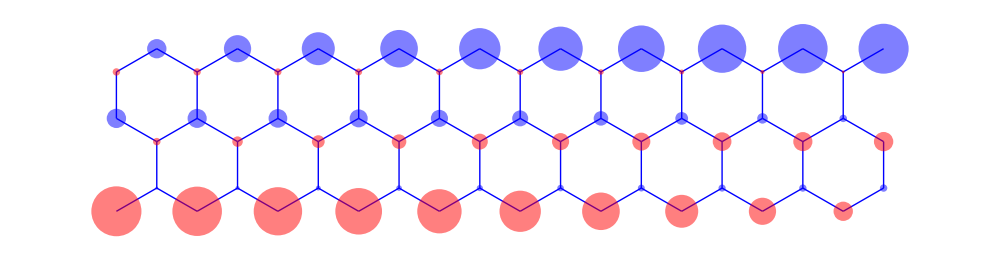

Vortex Case

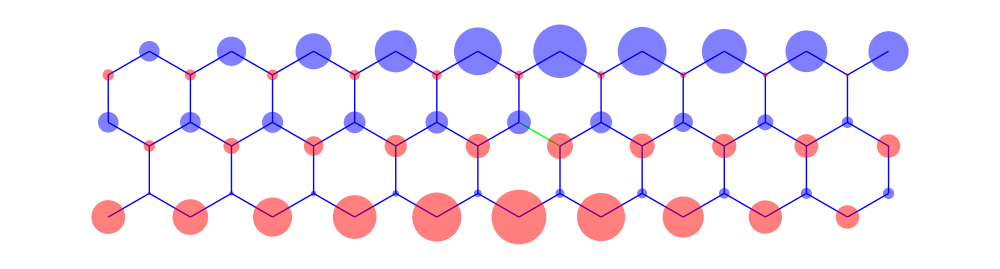

```mathematica
ClearAll
NumberOfSites = 6;
NumberOfRibbons = 10;
VortexIndex = 45;
VortexIndices = {35, 45};
points = 10;
HoppingTermLocations =  {};
m = 1;


(* Find the locations of all entries in energy matrix *)
For[j = 1, j < NumberOfRibbons * NumberOfSites, j++,
If[EvenQ[j],
{
If[OddQ[m] && (j / NumberOfSites) ≤ NumberOfRibbons - 1 , AppendTo[HoppingTermLocations,{j, j+NumberOfSites - 1}], Null ];
m +=1;
}
 ,
If[EvenQ[m] && (j / NumberOfSites) < NumberOfRibbons - 1&& m > 1,AppendTo[HoppingTermLocations,{j, j+NumberOfSites +1 }], Null ];
];
If[IntegerQ[j / NumberOfSites], m = 1, AppendTo[HoppingTermLocations, {j, j+1}]];
]


(* Energy Matrices for Vortex and Vortex Free Cases *)

(* Change this to be for a general number of vortices *)
EnergyMatrixVortex[t_] := SparseArray[  HoppingTermLocations-> Flatten[Append[{{Table[-t , {VortexIndex - 1}]}}, {{t},Table[-t , Length[HoppingTermLocations] - VortexIndex]}],2] , {NumberOfSites * NumberOfRibbons, NumberOfSites * NumberOfRibbons}] + Transpose[SparseArray[  HoppingTermLocations-> Flatten[Append[{{Table[-t , {VortexIndex - 1}]}}, {{t},Table[-t , Length[HoppingTermLocations] - VortexIndex]}],2], {NumberOfSites * NumberOfRibbons, NumberOfSites * NumberOfRibbons} ]]

EnergyMatrix[t_] := SparseArray[HoppingTermLocations -> Table[-t, Length[HoppingTermLocations]], {NumberOfSites * NumberOfRibbons, NumberOfSites * NumberOfRibbons}] + Transpose[ SparseArray[HoppingTermLocations -> Table[-t, Length[HoppingTermLocations]], {NumberOfSites * NumberOfRibbons, NumberOfSites * NumberOfRibbons}]];
 
(* Function for labelling x axis *)
frametickfunction[xmin_,xmax_]:={#,ToString[#/NumberOfSites]}&/@FindDivisions[{xmin,xmax,NumberOfSites}, NumberOfRibbons]


(* Calculate Eigenvalues and Eigenvectors of above matrices *)
EnergyVortexEigenvalues[t_] := Eigenvalues[N[EnergyMatrixVortex[t]]];
EnergyVortexEigenvectors[t_]:=Eigenvectors[N[EnergyMatrixVortex[t]]];

EnergyEigenvalues[t_] :=Eigenvalues[N[EnergyMatrix[t]]];
EnergyEigenvectors[t_]:=Eigenvectors[N[EnergyMatrix[t]]];

EvaluatedEigenvectors = EnergyEigenvectors[1/3];
EvaluatedVortexEigenvectors = EnergyVortexEigenvectors[1/3];

(* Plot Results *)
ListPlot[{EnergyEigenvalues[1/3]}, ImageSize->500]
ListLinePlot[{EvaluatedEigenvectors[[-1]]^2}, ImageSize->500,PlotRange->Full, Ticks->{frametickfunction[0,NumberOfSites * NumberOfRibbons], Automatic}]

ListPlot[{EnergyVortexEigenvalues[1/3]}, ImageSize->500]
ListLinePlot[{EvaluatedVortexEigenvectors[[-1]]^2}, ImageSize->500,PlotRange->Full, Ticks->{frametickfunction[0,NumberOfSites * NumberOfRibbons], Automatic}]


(*
For[i = 1, i < Length[EnergyEigenvectors[1/3]]+1,i++,ListLinePlot[Abs[N[EnergyEigenvectors[1/3][[i]]]]^2, ImageSize->200,PlotRange->Full,Ticks->{frametickfunction[0,NumberOfSites * NumberOfRibbons]}, GridLines->{Automatic, None}]//Print]
*)



(* Construct a Picture of the Lattice from the Matrix Elements of the Vortex Model *)
a=100;
Translation1 = {a/2,  a Sqrt[3] /2};
Translation2 = {-a/2, a Sqrt[3] /2};
RelativeBsite1 = {a/2, a Sqrt[3]/6};
RelativeBsite2 = {-a/2, a Sqrt[3]/6};
UpwardTranslation = {0, a /Sqrt[3]};
ConnectionPointLocation = {0,0};
AreaPrefactor  = 10000000;
GraphicsTable = {};
GraphicsTable3 = {};

(* I want to generate a lattice of points first, then add all of the connections *)
For[n = 1, n ≤ NumberOfRibbons, n++,
CenterOfTranslation = {0,0} + {(n-1)*a,0};
For[l = 1, l ≤ NumberOfSites, l+=2,
For[k = 1, k ≤ NumberOfSites * NumberOfRibbons, k++,
(* For each site in the ribbon, we want to parse over the whole row of the matrix *)
If[ EnergyMatrix[1][[ (l + ( (n-1) * NumberOfSites)),  k ]] ≠ 0 , 
{
If[0 < k - ((n-1) * NumberOfSites) && k -  ((n-1) * NumberOfSites)≤ NumberOfSites,
{
ConnectionPointLocation = {0,0} + {(n-1)*a, 0};
For[j = 1 , j < k - ((n-1)*NumberOfSites), j++,
If[ EvenQ[j], ConnectionPointLocation +=UpwardTranslation,If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
AppendTo[GraphicsTable, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}]
},
{
If[k - (n-1) * NumberOfSites ≤ 0,
{
ConnectionPointLocation = {0,0} + {(n-2)*a, 0};
For[j = 1 , j <  k  - ((n - 2) * NumberOfSites), j++,
If[ EvenQ[j], ConnectionPointLocation +=UpwardTranslation,If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
AppendTo[GraphicsTable, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}];
}
,
{
ConnectionPointLocation = {0,0} + {n*a, 0};
For[j = 1 , j < k - (n * NumberOfSites)  , j++,
If[ EvenQ[j], ConnectionPointLocation += UpwardTranslation, If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
AppendTo[GraphicsTable, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}];
}
]
}
];
}
,
Null
];
 ];

If[ EvenQ[(l+1)/2], CenterOfTranslation +=Translation2,CenterOfTranslation += Translation1];
]
];

(* I want to generate a lattice of points first, then add all of the connections *)
For[n = 1, n ≤ NumberOfRibbons, n++,
CenterOfTranslation = {0,0} + {(n-1)*a,0};
For[l = 1, l ≤ NumberOfSites, l+=2,
For[k = 1, k ≤ NumberOfSites * NumberOfRibbons, k++,
(* For each site in the ribbon, we want to parse over the whole row of the matrix *)
If[ EnergyMatrixVortex[1][[ (l + ( (n-1) * NumberOfSites)),  k ]] ≠ 0 , 
{
If[0 < k - ((n-1) * NumberOfSites) && k -  ((n-1) * NumberOfSites)≤ NumberOfSites,
{
ConnectionPointLocation = {0,0} + {(n-1)*a, 0};
For[j = 1 , j < k - ((n-1)*NumberOfSites), j++,
If[ EvenQ[j], ConnectionPointLocation +=UpwardTranslation,If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
If[EnergyMatrixVortex[1][[ (l + ( (n-1) * NumberOfSites)),  k ]] < 0,AppendTo[GraphicsTable3, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}],AppendTo[GraphicsTable3, {Thin, Green,Line[{CenterOfTranslation, ConnectionPointLocation}]}]]
}
,
{
If[k - (n-1) * NumberOfSites ≤ 0,
{
ConnectionPointLocation = {0,0} + {(n-2)*a, 0};
For[j = 1 , j <  k  - ((n - 2) * NumberOfSites), j++,
If[ EvenQ[j], ConnectionPointLocation +=UpwardTranslation,If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
If[EnergyMatrixVortex[1][[ (l + ( (n-1) * NumberOfSites)),  k ]] < 0,AppendTo[GraphicsTable3, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}],AppendTo[GraphicsTable3, {Thin, Green,Line[{CenterOfTranslation, ConnectionPointLocation}]}]]
}
,
{
ConnectionPointLocation = {0,0} + {n*a, 0};
For[j = 1 , j < k - (n * NumberOfSites)  , j++,
If[ EvenQ[j], ConnectionPointLocation += UpwardTranslation, If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
If[EnergyMatrixVortex[1][[ (l + ( (n-1) * NumberOfSites)),  k ]] < 0,AppendTo[GraphicsTable3, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}],AppendTo[GraphicsTable3, {Thin, Green,Line[{CenterOfTranslation, ConnectionPointLocation}]}]]
}
]
}
];
}
,
Null
];
 ];

If[ EvenQ[(l+1)/2], CenterOfTranslation +=Translation2,CenterOfTranslation += Translation1];
]
];


For[n = 0, n < NumberOfRibbons, n++,
CenterOfTranslation = {0,0} + {n*a, 0};
For[l = 1, l ≤  NumberOfSites, l++,
AppendTo[GraphicsTable, If[EvenQ[l], {Blue, Opacity[0.5], Disk[CenterOfTranslation, Abs[(AreaPrefactor * EvaluatedEigenvectors[[-1,(l + (n * NumberOfSites))]]^2)^(1/4)] ]}, {Red, Opacity[0.5], Disk[CenterOfTranslation, Abs[(AreaPrefactor * EvaluatedEigenvectors[[-1,(l + (n * NumberOfSites))]]^2)^(1/4)] ]}]];
If[ EvenQ[l], CenterOfTranslation +=UpwardTranslation,If[EvenQ[(l+1)/2], CenterOfTranslation += RelativeBsite2, CenterOfTranslation += RelativeBsite1]];
]
]

For[n = 0, n < NumberOfRibbons, n++,
CenterOfTranslation = {0,0} + {n*a, 0};
For[l = 1, l ≤  NumberOfSites, l++,
AppendTo[GraphicsTable3, If[EvenQ[l], {Blue, Opacity[0.5], Disk[CenterOfTranslation, Abs[(AreaPrefactor * EvaluatedVortexEigenvectors[[-1,(l + (n * NumberOfSites))]]^2)^(1/4)] ]}, {Red, Opacity[0.5], Disk[CenterOfTranslation, Abs[(AreaPrefactor * EvaluatedVortexEigenvectors[[-1,(l + (n * NumberOfSites))]]^2)^(1/4)] ]}]];
If[ EvenQ[l], CenterOfTranslation +=UpwardTranslation,If[EvenQ[(l+1)/2], CenterOfTranslation += RelativeBsite2, CenterOfTranslation += RelativeBsite1]];
]
]
Print["Vortex Free Case"]
Graphics[GraphicsTable, ImageSize->1000]
Print["Vortex Case"]
Graphics[GraphicsTable3, ImageSize->1000]
```

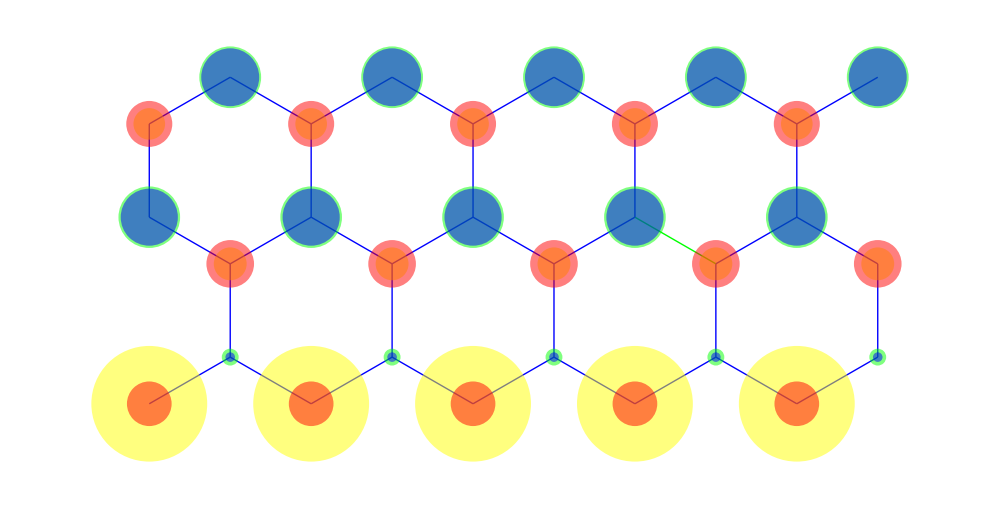

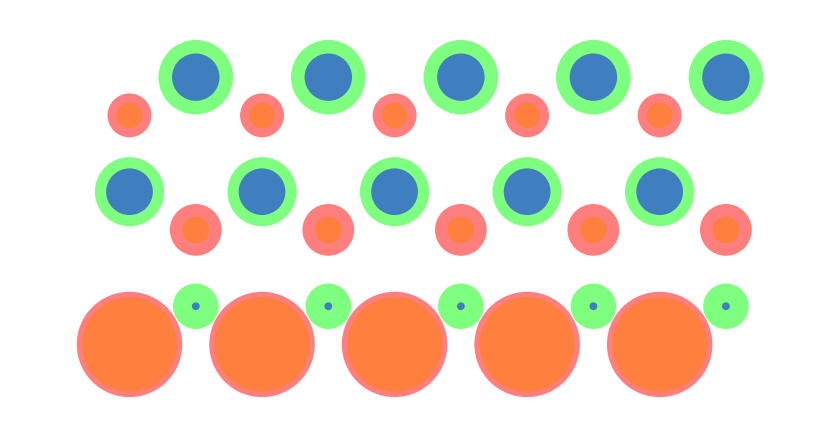

```mathematica
Clear[GraphicsTable, GraphicsTable3]

(* Construct a Picture of the Lattice from the Matrix Elements of the Vortex Model *)
a=100;
Translation1 = {a/2,  a Sqrt[3] /2};
Translation2 = {-a/2, a Sqrt[3] /2};
RelativeBsite1 = {a/2, a Sqrt[3]/6};
RelativeBsite2 = {-a/2, a Sqrt[3]/6};
UpwardTranslation = {0, a /Sqrt[3]};
ConnectionPointLocation = {0,0};
AreaPrefactor  = 10000000;
GraphicsTable = {};
GraphicsTable3 = {};

(* I want to generate a lattice of points first, then add all of the connections *)
For[n = 1, n ≤ NumberOfRibbons, n++,
CenterOfTranslation = {0,0} + {(n-1)*a,0};
For[l = 1, l ≤ NumberOfSites, l+=2,
For[k = 1, k ≤ NumberOfSites * NumberOfRibbons, k++,
(* For each site in the ribbon, we want to parse over the whole row of the matrix *)
If[ EnergyMatrix[1][[ (l + ( (n-1) * NumberOfSites)),  k ]] ≠ 0 , 
{
If[0 < k - ((n-1) * NumberOfSites) && k -  ((n-1) * NumberOfSites)≤ NumberOfSites,
{
ConnectionPointLocation = {0,0} + {(n-1)*a, 0};
For[j = 1 , j < k - ((n-1)*NumberOfSites), j++,
If[ EvenQ[j], ConnectionPointLocation +=UpwardTranslation,If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
AppendTo[GraphicsTable, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}]
},
{
If[k - (n-1) * NumberOfSites ≤ 0,
{
ConnectionPointLocation = {0,0} + {(n-2)*a, 0};
For[j = 1 , j <  k  - ((n - 2) * NumberOfSites), j++,
If[ EvenQ[j], ConnectionPointLocation +=UpwardTranslation,If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
AppendTo[GraphicsTable, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}];
}
,
{
ConnectionPointLocation = {0,0} + {n*a, 0};
For[j = 1 , j < k - (n * NumberOfSites)  , j++,
If[ EvenQ[j], ConnectionPointLocation += UpwardTranslation, If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
AppendTo[GraphicsTable, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}];
}
]
}
];
}
,
Null
];
 ];

If[ EvenQ[(l+1)/2], CenterOfTranslation +=Translation2,CenterOfTranslation += Translation1];
]
];

(* I want to generate a lattice of points first, then add all of the connections *)
For[n = 1, n ≤ NumberOfRibbons, n++,
CenterOfTranslation = {0,0} + {(n-1)*a,0};
For[l = 1, l ≤ NumberOfSites, l+=2,
For[k = 1, k ≤ NumberOfSites * NumberOfRibbons, k++,
(* For each site in the ribbon, we want to parse over the whole row of the matrix *)
If[ EnergyMatrixVortex[1][[ (l + ( (n-1) * NumberOfSites)),  k ]] ≠ 0 , 
{
If[0 < k - ((n-1) * NumberOfSites) && k -  ((n-1) * NumberOfSites)≤ NumberOfSites,
{
ConnectionPointLocation = {0,0} + {(n-1)*a, 0};
For[j = 1 , j < k - ((n-1)*NumberOfSites), j++,
If[ EvenQ[j], ConnectionPointLocation +=UpwardTranslation,If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
If[EnergyMatrixVortex[1][[ (l + ( (n-1) * NumberOfSites)),  k ]] < 0,AppendTo[GraphicsTable3, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}],AppendTo[GraphicsTable3, {Thin, Green,Line[{CenterOfTranslation, ConnectionPointLocation}]}]]
}
,
{
If[k - (n-1) * NumberOfSites ≤ 0,
{
ConnectionPointLocation = {0,0} + {(n-2)*a, 0};
For[j = 1 , j <  k  - ((n - 2) * NumberOfSites), j++,
If[ EvenQ[j], ConnectionPointLocation +=UpwardTranslation,If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
If[EnergyMatrixVortex[1][[ (l + ( (n-1) * NumberOfSites)),  k ]] < 0,AppendTo[GraphicsTable3, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}],AppendTo[GraphicsTable3, {Thin, Green,Line[{CenterOfTranslation, ConnectionPointLocation}]}]]
}
,
{
ConnectionPointLocation = {0,0} + {n*a, 0};
For[j = 1 , j < k - (n * NumberOfSites)  , j++,
If[ EvenQ[j], ConnectionPointLocation += UpwardTranslation, If[EvenQ[(j+1)/2], ConnectionPointLocation += RelativeBsite2, ConnectionPointLocation += RelativeBsite1]];
];
If[EnergyMatrixVortex[1][[ (l + ( (n-1) * NumberOfSites)),  k ]] < 0,AppendTo[GraphicsTable3, {Thin, Blue,Line[{CenterOfTranslation, ConnectionPointLocation}]}],AppendTo[GraphicsTable3, {Thin, Green,Line[{CenterOfTranslation, ConnectionPointLocation}]}]]
}
]
}
];
}
,
Null
];
 ];

If[ EvenQ[(l+1)/2], CenterOfTranslation +=Translation2,CenterOfTranslation += Translation1];
]
];


For[k = 1, k ≤ 1, k++,
GraphicsTable4 = {};
For[n = 0, n < NumberOfRibbons, n++,
CenterOfTranslation = {0,0} + {n*a, 0};
For[l = 1, l ≤  NumberOfSites, l++,
AppendTo[GraphicsTable4, If[EvenQ[l], {Green, Opacity[0.5], Disk[CenterOfTranslation, (AreaPrefactor * EvaluatedEigenvectors[[-k,l]]^2)^(1/4) ]}, {Yellow, Opacity[0.5], Disk[CenterOfTranslation, (AreaPrefactor* EvaluatedEigenvectors[[-k,l]]^2)^(1/4) ]}]];
If[ EvenQ[l], CenterOfTranslation +=UpwardTranslation,If[EvenQ[(l+1)/2], CenterOfTranslation += RelativeBsite2, CenterOfTranslation += RelativeBsite1]];
]
];

For[n = 0, n < NumberOfRibbons, n++,
CenterOfTranslation = {0,0} + {n*a, 0};
For[l = 1, l ≤  NumberOfSites, l++,
AppendTo[GraphicsTable4, If[EvenQ[l], {Blue, Opacity[0.5], Disk[CenterOfTranslation, (AreaPrefactor * EvaluatedVortexEigenvectors[[-k,l]]^2)^(1/4) ]}, {Red, Opacity[0.5], Disk[CenterOfTranslation, (AreaPrefactor * EvaluatedVortexEigenvectors[[-k,l]]^2)^(1/4) ]}]];
If[ EvenQ[l], CenterOfTranslation +=UpwardTranslation,If[EvenQ[(l+1)/2], CenterOfTranslation += RelativeBsite2, CenterOfTranslation += RelativeBsite1]];
]
];

Graphics[{GraphicsTable3, GraphicsTable4}, ImageSize->1000]//Print
]
```